```mathematica
SetDirectory["~/maths/ibmer/papers/mdgp/intro_dg"]
```

/Users/liberti/maths/ibmer/papers/mdgp/intro_dg

```mathematica
Get["ApproxRealize.m"]
```

```mathematica
G=Graph[{1<->2,1<->3,2<->3,2<->4,3<->4},VertexLabels->"Name",EdgeWeight->{2,2,1,1,1}]
```

-Graphics-

```mathematica
G1=RandomGraph[{10,30},EdgeWeight->RandomInteger[5,30]]
```

-Graphics-

```mathematica
n=Length[VertexList[G1]]
```

10

```mathematica
x=StochasticProximityEmbedding[G1, 2]
```

{{0.,0.},{-0.63795,-1.35558},{0.844768,0.89752},{1.17903,-1.0337},{-2.98991,-2.14348},{1.22398,0.554185},{-1.02019,1.14866},{-0.158311,2.20794},{0.136093,-2.23112},{2.37816,-1.60431}}

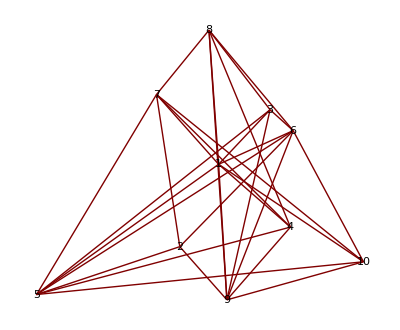

```mathematica
GraphPlot[G1, VertexLabeling->True, VertexCoordinateRules->x]
```

```mathematica
x3=StochasticProximityEmbedding[G1, 3]
```

{{0.,0.,0.},{-1.84275,-0.18525,-0.920342},{-0.26434,1.49632,-0.821986},{-0.534255,0.495373,1.28816},{-2.70904,-1.55888,-2.22515},{0.265327,1.64898,-0.22889},{0.40718,-0.167383,-1.60426},{0.670085,0.982227,-2.46802},{-2.37751,-0.041709,0.407889},{-1.71003,2.12806,1.16687}}

```mathematica
GraphPlot3D[G1, VertexLabeling->True, VertexCoordinateRules->x3]
```

-Graphics3D-

```mathematica
K=2
```

2

```mathematica
A=Normal[WeightedAdjacencyMatrix[G1]]
```

{{0,0,3,1,4,1,1,3,2,3},{0,0,0,0,1,2,3,0,1,0},{3,0,0,0,5,0,0,0,0,0},{1,0,0,0,5,0,3,4,1,0},{4,1,5,5,0,5,3,0,0,5},{1,2,0,0,5,0,0,3,5,2},{1,3,0,3,3,0,0,1,0,5},{3,0,0,4,0,3,1,0,5,0},{2,1,0,1,0,5,0,5,0,2},{3,0,0,0,5,2,5,0,2,0}}

```mathematica
B= EuclideanDistanceMatrix[x3]
```

{{0.,2.0681,1.72757,1.47993,3.8367,1.6858,1.66357,2.73951,2.4126,2.96891},{2.0681,0.,2.3084,2.65573,2.08323,2.87862,2.35164,3.17374,1.43902,3.11857},{1.72757,2.3084,0.,2.35106,4.15688,0.8097,1.95724,1.96135,2.88853,2.53863},{1.47993,2.65573,2.35106,0.,4.61443,2.06678,3.11314,3.97447,2.11209,2.01564},{3.8367,2.08323,4.15688,4.61443,0.,4.80856,3.4688,4.23494,3.0569,5.10856},{1.6858,2.87862,0.8097,2.06678,4.80856,0.,2.28274,2.3711,3.20133,2.4657},{1.66357,2.35164,1.95724,3.11314,3.4688,2.28274,0.,1.46179,3.43788,4.17502},{2.73951,3.17374,1.96135,3.97447,4.23494,2.3711,1.46179,0.,4.3136,4.49336},{2.4126,1.43902,2.88853,2.11209,3.0569,3.20133,3.43788,4.3136,0.,2.39363},{2.96891,3.11857,2.53863,2.01564,5.10856,2.4657,4.17502,4.49336,2.39363,0.}}

```mathematica
PartialEDMError[A, B]
```

```mathematica
y =Array[z, {n, K}]
```

{{z[1,1],z[1,2]},{z[2,1],z[2,2]},{z[3,1],z[3,2]},{z[4,1],z[4,2]},{z[5,1],z[5,2]},{z[6,1],z[6,2]},{z[7,1],z[7,2]},{z[8,1],z[8,2]},{z[9,1],z[9,2]},{z[10,1],z[10,2]}}

```mathematica
xx = DGPSystemApprox[G1, y, x]
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{33.4054,18.3732},{32.3107,17.8746},{33.2345,19.4235},{33.3533,17.9614},{31.3438,18.6278},{33.7625,18.369},{32.8916,19.4494},{33.7656,20.0125},{32.0754,18.6518},{32.824,17.1497}}

```mathematica
EuclideanDistanceMatrix[xx]
```

{{0.,1.26113,1.03941,0.972165,2.00135,0.799314,0.536724,1.81791,1.09389,1.7416},{1.26113,0.,0.472765,0.936526,1.385,1.22315,1.24707,0.588341,1.072,0.753517},{1.03941,0.472765,0.,0.464441,1.81058,0.774654,1.22808,1.02713,1.29345,0.703163},{0.972165,0.936526,0.464441,0.,2.23526,0.367922,1.34574,1.4847,1.59639,0.951644},{2.00135,1.385,1.81058,2.23526,0.,2.4162,1.57817,1.19419,0.945887,2.04536},{0.799314,1.22315,0.774654,0.367922,2.4162,0.,1.27615,1.79841,1.66398,1.31946},{0.536724,1.24707,1.22808,1.34574,1.57817,1.27615,0.,1.70088,0.632916,1.89901},{1.81791,0.588341,1.02713,1.4847,1.19419,1.79841,1.70088,0.,1.32587,0.917816},{1.09389,1.072,1.29345,1.59639,0.945887,1.66398,0.632916,1.32587,0.,1.82184},{1.7416,0.753517,0.703163,0.951644,2.04536,1.31946,1.89901,0.917816,1.82184,0.}}

```mathematica
PartialEDMError[A, EuclideanDistanceMatrix[xx]]
```

1.53841

```mathematica
(t=1) /; 2>3
```

1/;2>3

```mathematica
t
```

1

```mathematica
If[2>3, t=2, Null]
```

```mathematica
t
```

1